```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],21;;-1] & /@ republicans[[2;;31]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

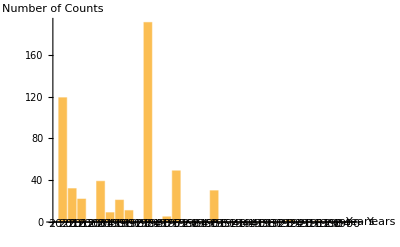

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

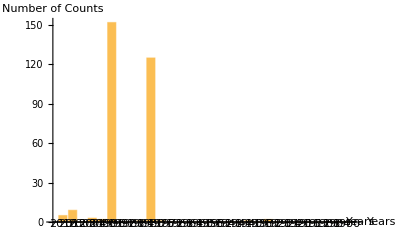

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
posnegtrain = ResourceData["Sample Data: Movie Review Sentence Polarity", "TrainingData"]
```

```mathematica
(*Let's think abt this*)
```

```mathematica
sentimentScore[text_,device_:"CPU"]:=With[{output=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"LastState","Output"}],TargetDevice->device]},Switch[Depth[output],2,output[[2389]],3,output[[All,2389]]]]
```

```mathematica
sentimentScore[RandomSample[TextSentences[Values[democratTexts][[1]]], 1]]
```

{-0.0764119}

```mathematica
Mean[Table[sentimentScore[s], {s, RandomSample[TextSentences[Values[democratTexts][[1]]], 200]}]]
```

$Aborted

```mathematica
(*up to here*)
```

```mathematica
libcons = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/liberal-conservative.csv", "Data", HeaderLines->1]
```

```mathematica
Counts[Head/@libcons[[All, 8]]]
```

<|String→12854|>

```mathematica
classlibcons = Table[StringReplace[ToString[s[[8]]], PunctuationCharacter:>""]->s[[2]], {s, Select[libcons, WordCount[#[[8]]] > 0 &]}]
```

```mathematica
encoder=NetModel["BERT Trained on BookCorpus and Wikipedia Data"]
```

NetChain[<2>]

```mathematica
subsetSize=1024*32;
```

```mathematica
indices=RandomSample[Range[Length[libcons]],Min[subsetSize,Length[libcons]]];
```

```mathematica
dataset2=Monitor[Table[Mean[encoder[libcons[[indices[[idx]]]][[1]]]]->libcons[[indices[[idx]]]][[2]],{idx,Length[indices]}],idx]
```

$Aborted

```mathematica
dataset2=Monitor[Table[libcons[[indices[[idx]]]][[1]]->libcons[[indices[[idx]]]][[2]],{idx,Length[indices]}],idx]
```

```mathematica
datasetDown=Values[Keys/@GroupBy[Thread[DimensionReduce[Keys[dataset2],2,Method->"TSNE"]->Values[dataset2]],Values]];
```

```mathematica
ListPlot[datasetDown]
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][dataset2];
```

```mathematica
{Length[trainSet],Length[testSet]}
```

{10283,2571}

```mathematica
libconsf = Classify[trainSet]
```

ClassifierFunction[…]

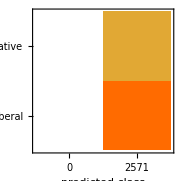
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 2571
Accuracy | (64.60.9) %
Accuracy baseline | (64.60.9) %
Geometric mean of probabilities | 0.522 ± 0.0029
Mean cross entropy | 0.65 ± 0.0056
Single evaluation time | 5.32 ms/example
Batch evaluation speed | 80.6 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[libconsf,testSet]
```

```mathematica
libconsf["I support donald trump because I agree with his ."]
```

Liberal